# Generate Skeleton v.2

## Prep

### Set up

```mathematica
SetDirectory[NotebookDirectory[]];
skmfile="Data/skel-w-msure-data/323-5_t35_proc_ma_skel.skMsure";
```

```mathematica
Needs["CornRootsFileReader`","Packages/CornRootsFileReader.wl"]
Needs["VisualizationFunctions`","Packages/VisualizationFunctions.wl"]
Needs["OperationFunctions`","Packages/OperationFunctions.wl"]
Needs["FairSimplify`","Packages/FairSimplify.wl"]
```

```mathematica
{vertices, edges, faces,edgeMeasure,faceMeasure}=
ParseSKMfile[skmfile];
{thickness,width,length}=Transpose@edgeMeasure;
```

### Smooth

After fairing 70 times, the zig-zag skeleton is very smoothed. We will see some visualizations later.

```mathematica
({v,e}=Fair2D[{vertices,edges},0.5,0.1,70])//Timing
```

{28.5151,{{{180.383,91.9006,94.5226},{155.061,121.944,131.848},11844,{201.147,97.6319,88.3945},{199.144,96.9136,91.487}},{{3,220},11849,{540,11848}}}}
 |  |  |  |

## Step 1: Duplicate v4984 <-> v4991

```mathematica
loopEdges=ExtractInfiniteEdges[e, length];
loopGraph=MapThread[#1<->#2&,Transpose@loopEdges];
groupedVertices=DisconnectGraph[loopGraph,"Vertices"];
groupedEdges=DisconnectGraph[loopGraph,"Data"];
```

```mathematica
gE=ExtractEdge[4984,4991,loopEdges]
```

{4984,8112,1711,8134,1664,10779,4954,8125,4948,8124,4991}

```mathematica
eStar=Partition[gE,2,1]
```

{{4984,8112},{8112,1711},{1711,8134},{8134,1664},{1664,10779},{10779,4954},{4954,8125},{8125,4948},{4948,8124},{8124,4991}}

```mathematica
e1={8131,4984};
e2={8113,4984};
e3={4991,8129}; 
e4={4991,8123};
```

```mathematica
{V1, E1, {thickness1, width1, length1}}=DuplicateEdge[e1,e2,e3,e4,eStar,v,e,{thickness,width,length}];
```

The topological structure is changed, although the 3D graph looks no difference.

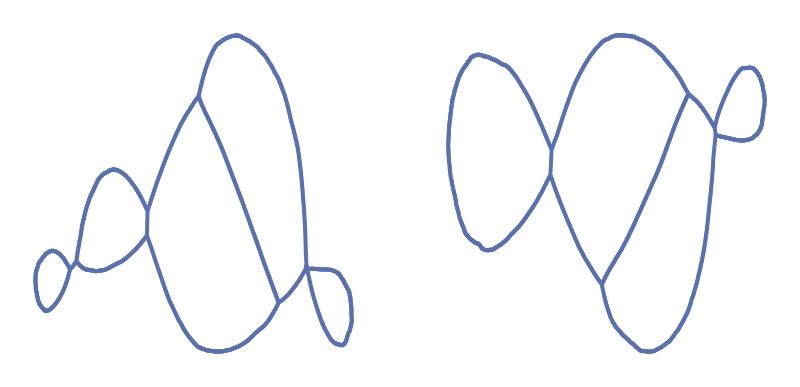

```mathematica
GraphicsRow[{Graph[loopGraph],Graph[ConvertListToEdge[ExtractInfiniteEdges[E1,length1]]]}]
```

## Step 2: Delete 5340 <-> 8108

```mathematica
metaEdge=Partition[ExtractEdge[5340,8108,E1],2,1]
```

{{5340,9974},{9974,2000},{2000,9975},{9975,5329},{5329,9976},{9976,1720},{1720,1993},{1993,8388},{8388,5341},{5341,8108}}

```mathematica
{E2,{thickness2, width2, length2}}=DeleteEdge[E1,Join[metaEdge,Reverse/@metaEdge],{thickness1, width1, length1}]
```

{{{3,220},{4,1038},{5,2749},{5,3685},{8,2233},{8,3570},{9,1546},{13,1374},{13,1820},{15,32},{15,3917},{21,1963},{21,5268},{23,1581},11824,{2935,11847},{539,11848},{540,11848},{11849,11850},{11850,11851},{11851,11852},{11852,11853},{11853,11854},{11854,11855},{11855,11856},{11856,11857},{11857,11858},{11858,11859}},1}
 |  |  |  |

```mathematica
ExtractInfinitePart[V1,E2,length2, Red]
```

-Graphics3D-

## Step 3: Reconnect v_1 and v_2

v1 = 520, v2 = 2257

```mathematica
{E3, {thickness3, width3, length3}}=ConnectEdge[520,2257,{E2,{thickness2,width2,length2}}]
```

{{{3,220},{4,1038},{5,2749},{5,3685},{8,2233},{8,3570},{9,1546},{13,1374},{13,1820},{15,32},{15,3917},{21,1963},{21,5268},{23,1581},11825,{539,11848},{540,11848},{11849,11850},{11850,11851},{11851,11852},{11852,11853},{11853,11854},{11854,11855},{11855,11856},{11856,11857},{11857,11858},{11858,11859},{520,2257}},{1}}
 |  |  |  |

```mathematica
all=VisualizeRootGraphics3D[V1,E3,Blue]
```

-Graphics3D-

Before we perform duplicate operator on the rest of graph, it’s very helpful to have a graphic that each meta-edge is colored into different ways. I wrote a function Rainbow that can generate color based on how many meta-edges we have.

```mathematica
Table[Rainbow[i],{i,2,10}]//TableForm
```

RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.857359, 0.131106, 0.132128] |  |  |  |  |  |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.513417, 0.72992, 0.440682] | RGBColor[0.857359, 0.131106, 0.132128] |  |  |  |  |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334] | RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334] | RGBColor[0.857359, 0.131106, 0.132128] |  |  |  |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.266122, 0.486664, 0.802529] | RGBColor[0.513417, 0.72992, 0.440682] | RGBColor[0.863512, 0.670771, 0.236564] | RGBColor[0.857359, 0.131106, 0.132128] |  |  |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.2484884, 0.3863264, 0.813373] | RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001] | RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004] | RGBColor[0.8935136, 0.6004149999999999, 0.2205464] | RGBColor[0.857359, 0.131106, 0.132128] |  |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.246296, 0.31595666666666666, 0.80044] | RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334] | RGBColor[0.513417, 0.72992, 0.440682] | RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334] | RGBColor[0.901627, 0.5398719999999999, 0.208366] | RGBColor[0.857359, 0.131106, 0.132128] |  |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.24882857142857143, 0.264202, 0.7825611428571428] | RGBColor[0.2888631428571429, 0.5431845714285714, 0.7666072857142857] | RGBColor[0.41993314285714284, 0.6952647142857142, 0.555374] | RGBColor[0.6215634285714287, 0.743557, 0.3500992857142857] | RGBColor[0.8241045714285714, 0.6995635714285714, 0.25042971428571426] | RGBColor[0.9023275714285715, 0.49078171428571427, 0.199022] | RGBColor[0.857359, 0.131106, 0.132128] |  | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.250728, 0.225386, 0.769152] | RGBColor[0.266122, 0.486664, 0.802529] | RGBColor[0.36048, 0.655759, 0.645692] | RGBColor[0.513417, 0.72992, 0.440682] | RGBColor[0.705038, 0.742591, 0.299167] | RGBColor[0.863512, 0.670771, 0.236564] | RGBColor[0.902853, 0.453964, 0.192014] | RGBColor[0.857359, 0.131106, 0.132128] | 
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.2641351111111111, 0.20142911111111111, 0.7458891111111111] | RGBColor[0.2563255555555556, 0.4309208888888889, 0.8085534444444444] | RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334] | RGBColor[0.4391281111111111, 0.7049679999999999, 0.52925] | RGBColor[0.5971805555555556, 0.7421848888888889, 0.36770955555555557] | RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334] | RGBColor[0.8801795555555555, 0.6316843333333333, 0.22766533333333333] | RGBColor[0.8973538888888889, 0.4182404444444444, 0.18500666666666665] | RGBColor[0.857359, 0.131106, 0.132128]

Because we already did two operations: 
	+ duplicate edge(4991, 4984; metaEdge id = 10) 
	+ delete edge(5340, 8108; metaEdge id = 11)
Then metaEdge 5, 10, 6, 7, 11 are not problems anymore. We only need to focus on the rest 1, 2, 3, 4, 8, 9, 12

```mathematica
coloredEdges=ColorMetaEdges3D[V1, groupedEdges⟦{1,2,3,4,8,9,12}⟧]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.246296, 0.31595666666666666, 0.80044],RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.901627, 0.5398719999999999, 0.208366],RGBColor[0.857359, 0.131106, 0.132128]}

-Graphics3D-

Vertices whose degree = 3 is usually very useful,  because in 3D, when two branches overlap each other, there will have a >-< shape structure. Let’s take a look.

```mathematica
vertexDegree3Position = SelectVerticesWithDegree[E3,3,"Edge Position"];
```

```mathematica
ShowIntersectionPointByVertexPosition[Show[all,coloredEdges], vertexDegree3Position,V1,E3]
```

-Graphics3D-

After zoom enough and check carefully, we find another meta-edge that need to be duplicated.

-Graphics3D-

Let’s do it.

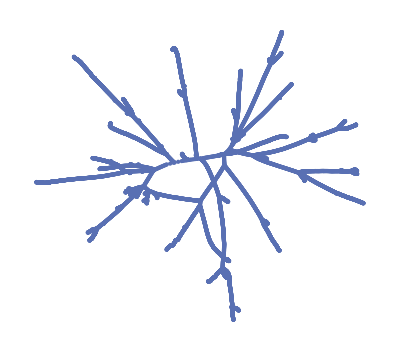

```mathematica
g3=Graph[ConvertListToEdge[E3]]
```

## Step 4: Duplicate 5672 <-> 2068

To perform duplicate, we need to collect {e_1, e_2, e_3, e_4, e}

```mathematica
vA=5672; vB=2068;
ShowVerticesID[Show[all,coloredEdges],Join[{vA,vB},nextVertex[vA,E3],nextVertex[vB,E3]],V1,E3]
```

-Graphics3D-

```mathematica
dupEdge=Partition[ExtractEdge[vA,vB,E3],2,1]
```

{{5672,7452},{7452,5671},{5671,8529},{8529,5653},{5653,6907},{6907,5666},{5666,11183},{11183,5669},{5669,11184},{11184,5670},{5670,8504},{8504,2192},{2192,8314},{8314,2068}}

But how to distinguish e_1, e_2, e_3, e_4 needs to go back to the Chimera picture. By observing, we can see purple line and yellow line are together, green line and blue line should be together.

-Graphics--Graphics3D-

```mathematica
e1= {7453, vA} ; e2 = {7451,vA};
e3 = {8395,vB}; e4 = {vB,8315};
```

```mathematica
{V4, E4, {thickness4, width4, length4}}=DuplicateEdge[e1,e2,e3,e4,dupEdge,V1,E3,{thickness3,width3,length3}]
```

{{{180.383,91.9006,94.5226},{155.061,121.944,131.848},11870,{206.697,130.512,100.921},{206.953,130.469,100.508}},{{3,220},{4,1038},11863,{11873,11874}},{1}}
 |  |  |  |

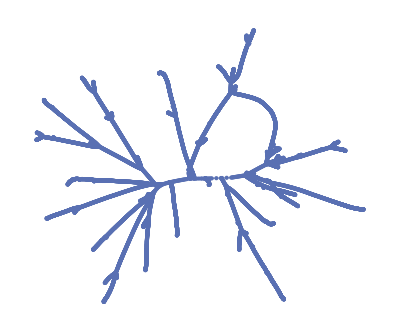

```mathematica
g4=Graph[ConvertListToEdge[E4]]
```

## Step 5: Delete 705 <-> 5890

```mathematica
ShowIntersectionPointByVertexPosition[Show[all,coloredEdges], vertexDegree3Position,V4,E4]
```

-Graphics3D-

```mathematica
metaEdge=Partition[ExtractEdge[5890,705,E4],2,1]
```

{{5890,11335},{11335,3467},{3467,9817},{9817,3442},{3442,9821},{9821,3440},{3440,9818},{9818,3441},{3441,9816},{9816,3438},{3438,8712},{8712,3444},{3444,9824},{9824,3443},{3443,9826},{9826,9825},{9825,9827},{9827,3478},{3478,9828},{9828,3439},{3439,9819},{9819,3454},{3454,9864},{9864,3476},{3476,9863},{9863,3481},{3481,9841},{9841,33},{33,7401},{7401,3482},{3482,7396},{7396,717},{717,7385},{7385,3480},{3480,9829},{9829,742},{742,9844},{9844,3494},{3494,9883},{9883,3499},{3499,7398},{7398,705}}

```mathematica
Clear[E5,thickness5,width5,length5]
```

```mathematica
{E5,{thickness5,width5,length5}}=DeleteEdge[E4,Join[metaEdge,Reverse/@metaEdge],{thickness4,width4,length4}]
```

{{{3,220},{4,1038},{5,2749},{5,3685},{8,2233},{8,3570},{9,1546},{13,1374},{13,1820},{15,32},{15,3917},{21,1963},{21,5268},11798,{11861,11862},{11862,11863},{11863,11864},{11864,11865},{11865,11866},{11866,11867},{11867,11868},{11868,11869},{11869,11870},{11870,11871},{11871,11872},{11872,11873},{11873,11874}},{1}}
 |  |  |  |

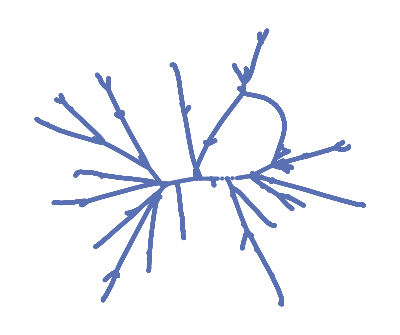

```mathematica
g5=Graph[ConvertListToEdge[E5]]
```

## Step 6: Delete Edge 7619 <->10737

```mathematica
edgePos3FromStep5=SelectVerticesWithDegree[E5,3,"Edge Position"];
```

```mathematica
ShowIntersectionPointByVertexPosition[Show[all,ExtractInfinitePart[V4,E5,length5,Red]], edgePos3FromStep5,V4,E5]
```

-Graphics3D-

```mathematica
metaEdge=Delete[Partition[ExtractEdge[7619,10737,E5],2,1],{{1},{-1}}]
```

{{4891,8098},{8098,8097},{8097,8099},{8099,4895},{4895,10739},{10739,4894}}

```mathematica
{E6,{thickness6,width6,length6}}=DeleteEdge[E5,Join[metaEdge,Reverse/@metaEdge],{thickness5,width5,length5}]
```

{{{3,220},{4,1038},{5,2749},{5,3685},{8,2233},{8,3570},{9,1546},{13,1374},{13,1820},{15,32},{15,3917},{21,1963},{21,5268},11792,{11861,11862},{11862,11863},{11863,11864},{11864,11865},{11865,11866},{11866,11867},{11867,11868},{11868,11869},{11869,11870},{11870,11871},{11871,11872},{11872,11873},{11873,11874}},{1}}
 |  |  |  |

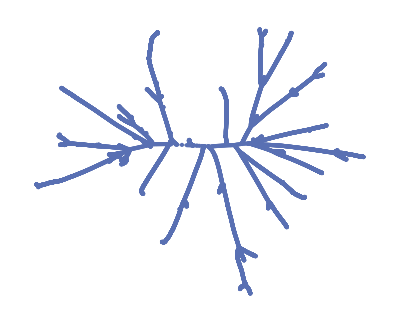

```mathematica
g6=Graph[ConvertListToEdge[E6]]
```

```mathematica
AcyclicGraphQ[g6]
```

True

So the final data is

```mathematica
acyclicSkeleton={V4,E6,{thickness6,width6,length6}}
```

{{{180.383,91.9006,94.5226},{155.061,121.944,131.848},11870,{206.697,130.512,100.921},{206.953,130.469,100.508}},{{3,220},{4,1038},11815,{11873,11874}},{1}}
 |  |  |  |